```mathematica
(*the following functions set things up, the only ones that should be used is SampleEvent for sampling individual energies, and SampleSpect for sampling from one of the saved spectra. The input for the former is eventkind which is either "ER" or "NR", and then an energy in keV, and then how many events you want to sample. SampleSpect gets a spectrum name, and the exposure you want to simulate (note that the signal is normalized to x-sec 10^(-47)cm^2 and 1TeV mass, and assumes MB distribution and 0.4GeV/cm^3, so if you want something smaller or larger, you have to multiply the exposure by the relevant quantity)*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*Load the S1 Bins for the individual energies*)
S1Bins=ToExpression["{"<>StringSplit[Import["SaveDetails.txt"],"\n"][[1]]<>"}"];
(*Load the S2 Bins for the individual energies*)
S2Bins=ToExpression["{"<>StringSplit[Import["SaveDetails.txt"],"\n"][[2]]<>"}"];
(*Load the Individual Energy*)
EList=<|"NR"->ToExpression["{"<>StringSplit[Import["SaveDetails.txt"],"\n"][[3]]<>"}"],"ER"->ToExpression["{"<>StringSplit[Import["SaveDetails.txt"],"\n"][[4]]<>"}"]|>;
(*How many simulations were used:*)
NSims=ToExpression[StringSplit[Import["SaveDetails.txt"],"\n"][[5]]];
(*Cumulative sum:*)
Cumsum[alist_]:=CompoundExpression[baf=0;Table[baf=baf+aterm;baf,{aterm,alist}]];
(*since I use the cumsum for making the CDF, I need to slightly change it so that it fits what I need*)
Cumsum2[alist_]:=CompoundExpression[Cumsumv0=Cumsum[alist];Transpose[{Flatten[{0,Cumsumv0+0.5,NSims}],Flatten[{Range[Length[Cumsumv0]+1]-1,0}]}]];
(*load a data from NR or ER from a specific numbered file*)
LoadData[EventKind_,Enumnow_]:=CompoundExpression[filename="Spectrum_"<>EventKind<>"_Enum="<>ToString[Enumnow]<>".txt";Map[ToExpression["{"<>#<>"}"]&][StringSplit[Import[filename],"\n"]]];
(*which number of energy does this energy match?*)
EnumFinder[EventKind_,Energy_]:=Round[Interpolation[Transpose[{EList[EventKind],Range[Length[EList[EventKind]]]-1}],Energy,InterpolationOrder->1]];
(*The actual thing you need to use. Eventkind is "ER" or "NR". Energy is the energy you want to sample. "howmanevents" is how many events you want to sample from that energy. The answer you get is {S1 bin,S2 bin}. However, if you get {-1,-1}, that means the event was not measured within our bins. The bins can be found by looking at the variables: S1Bins, S2Bins *)
SampleEvent[EventKind_,Energy_,howmanyevents_:1]:=If[(EventKind=="ER")||(EventKind=="NR"),If[Max[EList[EventKind]]<Energy,Print["The Energy you chose is too high, for " <>EventKind<>" events, the maximal allowed energy is "<>ToString[Max[EList[EventKind]]]];$Failed,If[Min[EList[EventKind]]>Energy,Print["The Energy you chose is too low, for " <>EventKind<>" events, the minimal allowed energy is "<>ToString[Min[EList[EventKind]]]];$Failed,Enumnow=EnumFinder[EventKind,Energy];EnergyDat=LoadData[EventKind,Enumnow];WhichBin=If[Length[EnergyDat]<2,Table[0,howmanyevents],Interpolation[Cumsum2[EnergyDat[[-1]]],InterpolationOrder->0][RandomInteger[NSims-1,howmanyevents]+1]];Table[If[WhichBinnow==0,{-1,-1},{S1Bins[[EnergyDat[[1,WhichBinnow]]]],S2Bins[[EnergyDat[[2,WhichBinnow]]]]}],{WhichBinnow,WhichBin}]]],Print["EventKind has to be either the string ER or the string NR."];$Failed];
(*load the S1 and S2 bins saved for the spectra (in practice I used the same for this and for the energy sampler):*)
S1BinsSpectra=Import["S1Bins.csv"][[2;;]];
S2BinsSpectra=Import["S2Bins.csv"][[2;;]];
(*loading the spectra (note that I don't include radon:*)
AllSpectra=<|"sig"->Import["sig.csv"][[2;;,2;;]],"Bkg_NR_solarnu"->Import["Bkg_NR_solarnu.csv"][[2;;,2;;]],"Bkg_NR_othernu"->Import["Bkg_NR_othernu.csv"][[2;;,2;;]],"Bkg_ER_solarnu"->Import["Bkg_ER_solarnu.csv"][[2;;,2;;]]|>;
AllSpectra["Bkg_All"]=AllSpectra["Bkg_NR_othernu"]+AllSpectra["Bkg_ER_solarnu"]+AllSpectra["Bkg_NR_solarnu"];
SampleSpectrum[SpectName_,Exposure_]:=Table[Table[If[bin==0,0,RandomVariate[PoissonDistribution[bin*Exposure]]],{bin,binrow}],{binrow,AllSpectra[SpectName]}];
```

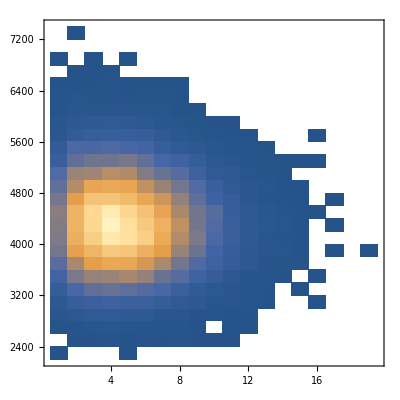

```mathematica
DensityHistogram[Select[#[[1]]>0&][SampleEvent["ER",2,100000]],{20,20}]
```

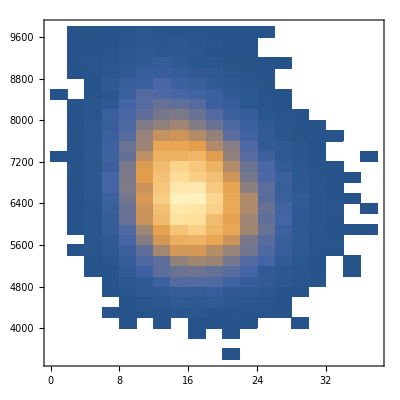

```mathematica
DensityHistogram[Select[#[[1]]>0&][SampleEvent["ER",4,100000]],{20,20}]
```

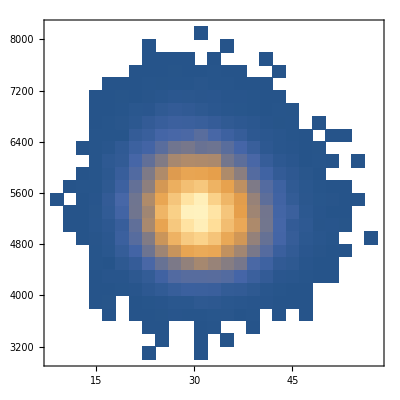

```mathematica
DensityHistogram[Select[#[[1]]>0&][SampleEvent["NR",26,100000]],{20,20}]
```

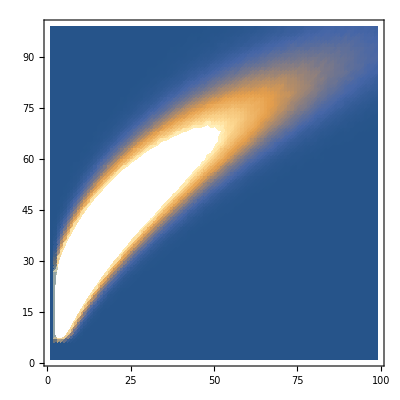

```mathematica
ListDensityPlot[Transpose[AllSpectra["sig"]]]
```

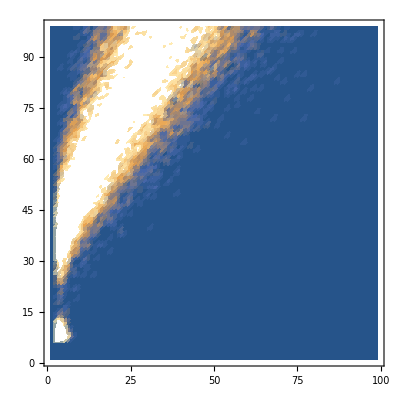

```mathematica
ListDensityPlot[Transpose[SampleSpectrum["Bkg_All",1500]]]
```